```mathematica
2+2
```

4

```mathematica
2+2
```

4

```mathematica
ClearAll[u,t,x,c,x0,xmin,xmax,tmax];

c=1;
x0=-10;
xmin=-30;
xmax=30;
tmax=20;
```

```mathematica
eq=D[u[t,x],t]==-D[u[t,x],{x,3}]+6 u[t,x] D[u[t,x],x];
```

```mathematica
DSolve[Derivative[1,0][u][t,x]==6 u[t,x] Derivative[0,1][u][t,x]-Derivative[0,3][u][t,x],{u[t,x],u[t,x],u[t,x]},{t,x}]
```

DSolve::nlpde: 非線形偏微分方程式の解が要求されました．特殊解の構築を試みています．

{{u[t,x]→(C[1]-8 C[2]^3+12 C[2]^3 Tanh[t C[1]+x C[2]+C[3]]^2)/(6 C[2])}}

```mathematica
ic=u[0,x]==(c/2) Sech[(Sqrt[c]/2) (x-x0)]^2;
```

```mathematica
FindRoot[u[0,x]==1/2 Sech[(10+x)/2]^2,{{x,1}}]
```

FindRoot::nlnum: {x} = {1.}において，関数の値{-0.0000334023+u[0.,1.]}は次元{1}の数値のリストではありません．

FindRoot[u[0,x]==1/2 Sech[(10+x)/2]^2,{{x,1}}]

```mathematica
bc={u[t,xmin]==0,u[t,xmax]==0,Derivative[0,1][u][t,xmin]==0};
```

```mathematica
DSolve[{u[t,-30]==0,u[t,30]==0,Derivative[0,1][u][t,-30]==0},{u[t,-30]},{t}]
```

DSolve::deqx: 与えられた方程式は指定の関数の微分方程式でも積分方程式でもありません．

DSolve[{u[t,-30]==0,u[t,30]==0,u^(0,1)[t,-30]==0},{u[t,-30]},{t}]

```mathematica
sol=NDSolveValue[{eq,ic,bc},u,{t,0,tmax},{x,xmin,xmax}];
```

NDSolveValue::ndsz: t == 0.141348において，刻み幅は実質的にゼロとなります．特異性または硬い系の可能性があります．

NDSolveValue::eerr: 警告：t = 0.141348において独立変数xの方向にスケールされた355134.の局所空間誤差推定が指定の許容誤差範囲を大きく超えています．233ポイントの格子間隔は，希望の精度または確度を達成するには大きすぎる可能性があります．特異性が形成されたかもしれません．もしくはMaxStepSizeまたはMinPointsメソッドオプションを用いてより小さな格子間隔を指定することができます．

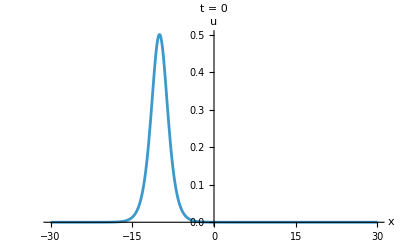

```mathematica
Plot[Evaluate[sol[0,x]],{x,xmin,xmax},PlotRange->All,AxesLabel->{"x","u"},PlotLabel->"t = 0"]
```